Quantum Master Equation

General Formpaclet:QuantumMob/Q3/tutorial/QuantumMasterEquation#829965404 | Solution Methodspaclet:QuantumMob/Q3/tutorial/QuantumMasterEquation#633590980
Derivationpaclet:QuantumMob/Q3/tutorial/QuantumMasterEquation#1028020285 | Examplespaclet:QuantumMob/Q3/tutorial/QuantumMasterEquation#1366817080

See also Section 5.4 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

Consider an open quantum system interacting with its environment. In general, the dynamical process at a given time depends on the whole history, and it is formidable to mathematically describe such dynamics.

Fortunately, under many physically relevant conditions, one can safely ignore the history effect. Within the so-called Markov approximation, the quantum operation governing the evolution of density operator ρ(t) can be reformulated in a differential form and the resulting equation is called the quantum master equation.

Supermappaclet:QuantumMob/Q3/ref/SupermapQuantumMob Package Symbol | Represents a supermap
ChoiMatrixpaclet:QuantumMob/Q3/ref/ChoiMatrixQuantumMob Package Symbol | Choi matrix corresponding to a supermap
LindbladSupermappaclet:QuantumMob/Q3/ref/LindbladSupermapQuantumMob Package Symbol | Represents a supermap generating the dynamical semigroup corresponding to a quantum master equation
LindbladSolvepaclet:QuantumMob/Q3/ref/LindbladSolveQuantumMob Package Symbol | Solves the quantum master equation
NLindbladSolvepaclet:QuantumMob/Q3/ref/NLindbladSolveQuantumMob Package Symbol | Numerically solves the quantum master equation
LindbladConvertpaclet:QuantumMob/Q3/ref/LindbladConvertQuantumMob Package Symbol | Converts a quantum master equation for density matrix to a conventional set of differential equations for vectorial form of the density matrix
LindbladSimulatepaclet:QuantumMob/Q3/ref/LindbladSimulateQuantumMob Package Symbol | Solve a quantum master equation using the quantum jump approach (Monte Carlo method).

Functions to help study quantum master equations.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
Needs["QuantumMob`Q3`"]
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol A will be used to denote qudits and operators acting on them.

```mathematica
Let[Qubit,S]
Let[Qudit,A]
```

General Form

Within the Markov approximation, the density operator ρ(t) satisfies a differential equation of the form,

dρ/dt=ℒ(ρ),

which is called the quantum master equation or Lindblad equation. Here, the superoperator ℒ defined by

ℒ(ρ):=-ⅈ[H,ρ]+Σ_μ(L_μ ρ L_μ^†-1/2 L_μ^†L_μ ρ-1/2 ρ L_μ^†L_μ) ,

generates the quantum Markovian dynamics and is called the Lindblad generator. The Hermitian operator H in the above equation describes the unitary part of the dynamics. For this reason, H is often called the effective Hamiltonian of the system, but in general it is not the same as the Hamiltonian when the system is isolated. The operators L_μ are responsible for the non-unitary dynamics and are called the Lindblad operators or quantum jump operators.

It is also customary to rewrite the Lindblad generator into the form

ℒ(ρ):=-ⅈ[H,ρ]-{G,ρ}+Σ_μ L_μ ρ L_μ^† ,

where

G:=1/2 Σ_μ L_μ^†L_μ .

Interestingly, ignoring the last term in the quantum jump operators, the solution to the approximate quantum master equation,

dρ/dt≈-ⅈ[H,ρ]-{G,ρ} ,

is simply given by

ρ(t)≈ⅇ^(-ⅈt H_non)ρ(0)ⅇ^(+ⅈt H_non^†) ,

which resembles the unitary dynamics with Hamiltonian H replaced with the effective non-Hermitian Hamiltonian

H_non:=H-ⅈG .

The additional term in G of the non-Hermitian Hamiltonian makes a significant difference in the evolution governed  ⅇ^(-ⅈt H_non) since it causes damping and leads to irreversible population loss in the eigenstates of H. To put it in another way, probability is not conserved any longer,

Tr[ⅇ^(-ⅈt H_non)ρ(0)ⅇ^(+ⅈt H_non^†)]=Tr[ρ(0)ⅇ^(-G+ⅈtH)ⅇ^(-G-ⅈtH)]<1 ,

because G is positive. In this sense, we call G the effective damping operator. Physically, other processes described by Lindblad operators L_μ  account for the loss in probability.

Although the non-Hermitian Hamiltonian approach does not explain all decoherence processes, it lays out an intuitively appealing picture of open systems and has been widely used to describe the effects of a finite life time of (effective) energy levels. The non-Hermitian Hamiltonian also provides a good starting point for various more elaborate methods to investigate decoherence processes. A common example is the so-called quantum jump approach. It is an approximate method to solve the quantum master equation combining the aforementioned non-unitary evolution due to the non-Hermitian Hamiltonian and the “quantum jumps” due to the quantum jump operators L_μ (Dum et al., 1992; Plenio and Knight, 1998).

Derivation

It is straightforward to derive the quantum master equation starting from the Kraus representation under the Markov assumption (see, e.g., Breuer and Petruccione (2002) for details). Here, we take a heuristic approach, which is more useful to understand the underlying physics. More common approach is to reduce, often approximately, the unitary dynamics of the total system consisting of the system and environment (see also Section 5.2.3) to the quantum master equation for the system only. Some examples including perturbative methods are discussed in Breuer and Petruccione (2002).

Consider an infinitesimal elapse δt of time from t to t':=t+δt. The density operator ρ(t') is related to ρ(t) by the Kraus representation

ρ(t')=Σ_μ F_μ(δt)ρ(t) F_μ^†(δt) ,

where we have imposed the Markovian approximation.  For δt≈0, it is physically required that ρ(t')≈ρ(t). This implies that one and only one of F_μ(δt) must approach the identity operator I. Let us denote it by F_0(δt). Up to the first order in δt,

F_0(δt)≈I-ⅈδt L_0 ,

where the additional factor -ⅈ is completely arbitrary at this stage but is introduced here for later convenience. The rest should vanish F_μ(δt)→0 for any μ≠0. Since we physically expect that ρ(t')≈ρ(t)+𝒪(δt), F_μ(δt) must vanish like √δt with δt so that F_μ(δt)ρ(t)F_μ^†(δt)≈𝒪(δt). We put

F_μ(δt)≈√δt L_μ  (μ≠0) .

Since L_μ (μ≠0) directly proportional to F_μ, they are all traceless and mutually orthogonal; i.e., Tr[L_μ^†L_μ]=0 for all μ≠ν. Putting these approximations back into the equation for ρ(t') at the beginning of this section leads to

ρ(t+δt)≈(I-ⅈδt L_0)ρ(t)(I-ⅈδt L_0)^†+δt Σ_(μ=1)^(d^2-1)L_μ ρ(t)L_μ^†≈ρ(t)-ⅈδt[L_0 ρ(t)-ρ(t)L_0^†]+δt Σ_(μ=1)^(d^2-1)L_μ ρ(t)L_μ^† .

The conservation of probability then implies that

L_0-L_0^†=-ⅈ Σ_(μ=1)^(d^2-1)L_μ^†L_μ .

This suggests that it will be convenient to split L_0 into the Hermitian and anti-Hermitian parts as

L_0=H-ⅈ G ,

which is identical to the non-Hermitian Hamiltonian as we already mentioned above. Indeed, the anti-Hermitian part, -ⅈG, is then fixed by operators L_μ with μ≠0 through the relation

G:=1/2 Σ_(μ=1)^(d^2-1)L_μ^†L_μ ,

where the Hermitian part H remains arbitrary and is determined only by F_0, which is linearly independent of any L_μ with μ≠0. In passing, it is important to note that G is positive, and as previously remarked, the probability conservation breaks down in the dynamics governed by the non-Hermitian Hamiltonian H_non (or, equivalently, L_0).

Finally, putting Equations (14) and (15) into Equation (12) leads to the desired equations (2) or, equivalently, (3). Note that in this particular derivation, Lindblad operators L_μ turn out to be traceless and mutually orthogonal automatically. Here, these properties inherit from the orthogonality of Kraus elements F_μ.

Solution Methods

### Integrating the Differential Equation

LindbladSolvepaclet:QuantumMob/Q3/ref/LindbladSolveQuantumMob Package Symbol | Solves the quantum master equation
NLindbladSolvepaclet:QuantumMob/Q3/ref/NLindbladSolveQuantumMob Package Symbol | Numerically solves the quantum master equation

The Lindblad equation is a linear equation without an explicit time dependence, and it can always be solved by means of common methods for linear differential equations. More explicitly, in the standard basis, the Lindblad equation can be written as

(ρ̇)_jk=Σ_j'k' M_(jk;j'k')ρ_j'k'

wit

M_(jk;j'k'):=-ⅈ(H_jj' δ_kk'-δ_jj' H_kk')-(G_jj' δ_kk'+δ_jj' G_kk')+Σ_μ L_(μ;jj')L_(μ;kk')^* .

Regarding μ:=(jk) and ν:=(j'k') as collective indices, the differential equation above reads as

(ρ̇)_μ=Σ_ν M_μν ρ_ν  ,

which is a typical first-order differential equation for the column vector ρ_ν.

Technically, the differential equation (18) is not adequate yet to solve because of the conditions that ρ^†=ρ and Tr[ρ]=1; that is, the components ρ_ij are not independent of each other. These conditions are reflected in the fact that the determinant of the matrix M is always zero.

For example, consider a single-qubit system. Suppose that the Lindblad equation is characterized by the effective Hamiltonian

H=1/2 Ω S^Z+1/2 Δ S^X

and the quantum jump operators √(Γ_±)S^±. In the matrix form, the quantum master equation is given by

d/dt(ρ_11
ρ_12
ρ_21
ρ_22)=1/2(-2 Γ_- | ⅈΔ | -ⅈΔ | 2 Γ_+
ⅈΔ | -Γ_--Γ_+-2ⅈΩ | 0 | -ⅈΔ
-ⅈΔ | 0 | -Γ_--Γ_++2ⅈΩ | ⅈΔ
2 Γ_- | -ⅈΔ | ⅈΔ | -2 Γ_+)(ρ_11
ρ_12
ρ_21
ρ_22)

Imposing the conditions ρ^†=ρ and Tr[ρ]=1, the above equation reads as

d/dt(ρ_11
Re ρ_21
Im ρ_21)=1/2(-2Γ | 0 | 0
0 | -Γ/2 | -ⅈ Γ/2
-ⅈΔ | -ⅈ Ω | -Ω)(ρ_11
Re ρ_21
Im ρ_21)+(Γ_+
0
Δ/2) ,

where Γ:=Γ_++Γ_-. It is a typical inhomogeneous first-order differential equation and can be solved using the standard methods. If necessary, various numerical methods can also be applied.  This method is extensively discussed in Blum (2012) .

In the above discussion, the constraints ρ^†=ρ and Tr[ρ]=1 have been handled in an ad hoc fashion. More systematic and efficient way is explained in the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7.

#### Example

```mathematica
Needs["QuantumMob`Q3`"]
```

Let us consider a single qubit and solve a master equation specified in the Pauli operators.

```mathematica
Let[Qubit,S]
```

Set an initial state.

```mathematica
in=(1+S[1])/2;
in//MatrixForm
```

1/2 (1+S^X)

Take an effective Hamiltonian.

```mathematica
opH=S[3];
```

Take the quantum jump operators that are responsible of particular quantum decoherence processes.

```mathematica
Let[Real,Γ]
opL={Sqrt[Γ["+"]] S[4],Sqrt[Γ["-"]]S[5]}
```

{S^+ √(Γ_(,,+)),S^- √(Γ_(,,-))}

Solve the quantum master equation.

```mathematica
Clear[rho]
rho[t_]=Block[
{ops=Prepend[opL,opH],
Γ},
Γ["+"]=.3;
Γ["-"]=.7;
LindbladSolve[ops,init,t]//Chop
];
```

For more detailed analysis, it is useful to examine the Lindblad generator, a supermap generating the quantum master equation.

```mathematica
spr=LindbladSupermap[opH, opL]
```

LindbladSupermap[…]

Take a look at the way the Lindblad generator acts, say, on the initial quantum state.

```mathematica
new=spr[in]
```

S^Y+1/4 S^X (-Γ_(,,-)-Γ_(,,+))+1/2 S^Z (-Γ_(,,-)+Γ_(,,+))

This is a slightly different (yet equivalent) way to specify the quantum master equation..

```mathematica
Clear[rho]
rho[t_]=Block[
{ops=Prepend[opL,opH],
Γ},
Γ["+"]=.3;
Γ["-"]=.7;
LindbladSolve[spr,init,t]//Chop
];
```

Take a look at the solution as a function of time.

```mathematica
rho[t]
```

0.5+(-0.2+0.2 ⅇ^(-1. t)) S^Z

For a physical interpretation, it is useful to get the Bloch vector corresponding to the density operator.

```mathematica
{avgX[t_],avgY[t_],avgZ[t_]}=Coefficient[Elaborate@rho[t],#]&/@S@{1,2,3}
```

{0,0,-0.2+0.2 ⅇ^(-1. t)}

Plot each component of the Bloch vector as a function of time.

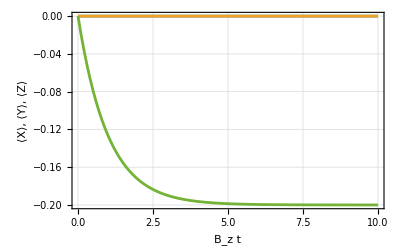

```mathematica
data=Transpose@Table[
{{t,avgX[t]},{t,avgY[t]},{t,avgZ[t]}},
{t,0,10,0.1}
];
ListLinePlot[data,
FrameLabel->{"B_z t","⟨X⟩, ⟨Y⟩, ⟨Z⟩"}
]
```

### Quantum Jump Approach

LindbladSimulatepaclet:QuantumMob/Q3/ref/LindbladSimulateQuantumMob Package Symbol | Solve a quantum master equation using the quantum jump approach (Monte Carlo method).

Integrating quantum master equation gets quickly intractable as the system increases in size. For example, for a system of n qubits, one has to deal with an order of 4^n×4^nmatrix; see Equations (16) and (17). The required memory is simply too large for most available computers. This is where the quantum jump approach  becomes extremely useful.

To understand the idea behind the quantum jump approach (Plenio and Knight, 1998https://doi.org/10.1103/RevModPhys.70.101), note that for a short elapse δt of time from t to t+δt, the density operator evolves as

ρ(t+δt)≈(I-ⅈδt L_0)ρ(t)(I-ⅈδt L_0)^†+δt Σ_(μ=1)^(d^2-1)L_μ ρ(t)L_μ^†≈U_non(δt)ρ(t)U_non^†(δt)+δt Σ_(μ=1)^(d^2-1)L_μ ρ(t)L_μ^† ,

where U_non(t) is the non-unitary time-evolution operator associated with the effective non-Hermitian Hamiltonian H_non; that is,

U_non(t):=ⅇ^(-ⅈt H_non) .

We have ignored the term of the second and higher orders in δt.

Conceptually, the key observation is that each term in Equation (19), U_non(δt)ρ(t)U_non^†(δt) or δt L_μ ρ(t)L_μ^†, represents a possible quantum state that is determined randomly with probability

P_0:=Tr[U_non(δt)ρ(t)U_non^†(δt)]

or

P_μ:=Tr[δt L_μ ρ(t)L_μ^†].

This means that to generate a trajectory of quantum state in the Hilbert space, we may just follow the spirit of Monte Carlo method and randomly apply δ F_0:=U_non(δt) or δ F_μ:=√δt L_μ with aforementioned probability at each time step t_k:=kδt. For example, starting with an initial pure state in,

ψ(t_0)=in,
ψ(t_1)=(δ F_0)in,
ψ(t_2)=(δ F_2)(δ F_0)in,
ψ(t_3)=(δ F_0)(δ F_2)(δ F_0)in,
ψ(t_4)=(δ F_1)(δ F_0)(δ F_2)(δ F_0)in,
…

is a possible trajectory. By repeating the same procedure, one can realize many trajectories. The density matrix ρ(t_k) at each time step t_k can be obtained by taking the statistical mixture from all resulting trajectories,

ρ(t_k)=Σ_trajectories ψ(t_k)ψ(t_k) .

Technically, the key advantage of the quantum jump approach is that it only requires memory to store a complex vector of 2^n components for updating the state at each time step. Additional memory is needed to store the trajectories, but for the trajectory data, one can also utilize external storage.

#### Example

```mathematica
Needs["QuantumMob`Q3`"]
```

Let us consider a system of qubits.

```mathematica
Let[Qubit,S]
```

Take an effective Hamiltonian.

```mathematica
opH=S[3]
```

S^Z

Consider the bit-flip noises as quantum jump operators.

```mathematica
Let[Real,Γ]
opL={Sqrt[Γ["+"]] S[4],Sqrt[Γ["-"]]S[5]}
```

{S^+ √(Γ_(,,+)),S^- √(Γ_(,,-))}

Take an initial state.

```mathematica
in=(Ket[]+Ket[S->1])/Sqrt[2]//KetRegulate
```

(0_(,,S)+1_(,,S))/(√2)

Pick the time slices at which the trajectory points are fixed.

```mathematica
tt=Range[0,10,0.05];
```

Simulate the Lindblad equation using the quantum jump approach.

```mathematica
EchoTiming[
data=Block[
{Γ},
Γ["+"]=.3;
Γ["-"]=.7;
LindbladSimulate[opH,opL,in,tt,
"Samples"->100]
];
]
```

0.205867

Construct the density matrix at each times. Again, notice Transposepaclet:ref/Transpose here; for the form of the output data, see the Details and Options section section above.

```mathematica
rho=Mean/@Map[Dyad[#,#]&,Transpose@data,{2}];
Dimensions[rho]
```

{201,2,2}

As an example, calculate the averages of the Pauli X, Y, and Z operators.

```mathematica
II=Transpose@{tt,Map[Tr[#]&,rho]};
XX=Transpose@{tt,Map[Tr[ThePauli[1].#]&,rho]};
YY=Transpose@{tt,Map[Tr[ThePauli[2].#]&,rho]};
ZZ=Transpose@{tt,Map[Tr[ThePauli[3].#]&,rho]};
ListPlot[{XX,YY,ZZ},
Joined->True,
FrameLabel->{"B_z t","⟨X⟩, ⟨Y⟩, ⟨Z⟩"},
PlotLegends->Automatic,
PlotRange->All]
```

-Graphics-

Examples

(to be completed)

### Phase Damping

### Amplitude Damping

### Depolarization Damping

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Noise and Decoherence
▪Quantum Information Systems with Q3

| Related Links
▪H.-P. Breuer and F. Petruccione (2002)https://doi.org/10.1093/acprof:oso/9780199213900.001.0001, The Theory of Open Quantum Systems (Oxford University Press, 2002).
▪D. A. Lidar, Z. Bihary, and K. B. Whaley, Chemical Physics 268, 35 (2001)https://doi.org/10.1016/S0301-0104(01)00330-5, "From completely positive maps to the quantum Markovian semigroup master equation."
▪M. B. Plenio and P. L. Knight (1998)https://doi.org/10.1103/RevModPhys.70.101, Review of Modern Physics 70, 101 (1998), "The quantum- jump approach to dissipative dynamics in quantum optics."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).